```mathematica
(*SetDirectory["..."];*)
Remove["Global`*"]
```

# Example 1: Competition and Collaboration

## Zebras and Lions 1: Slightly above the equilibrium point (zebras start with 1/3+something)

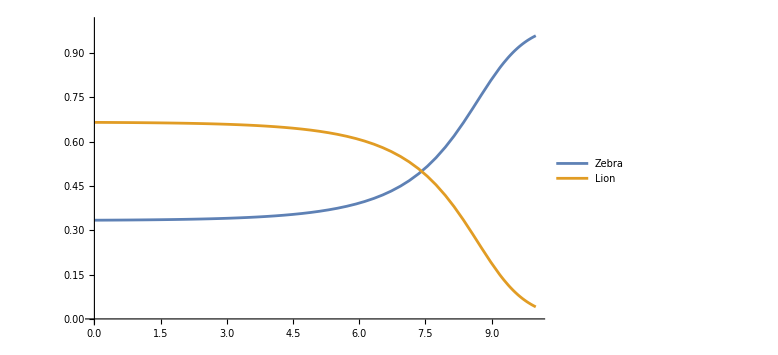

```mathematica
ClearAll[M,fA,fB,tmax,No,x,y];
M={{5,0},{3,1}};
x0=1/3+0.001;
phi[t]:=fA[x[t],y[t]]*x[t]+fB[x[t],y[t]]*y[t];
fA[x_,y_]:=( M[[1,1]]*x+M[[1,2]]*y);
fB[x_,y_]:=( M[[2,1]]*x+M[[2,2]]*y);
tmax=400;
soln=First@NDSolve[{x'[t]==fA[x[t],y[t]]*x[t]-phi[t]*x[t],y'[t]==fB[x[t],y[t]]*y[t]-phi[t]*y[t],x[0]==x0,y[0]==1-x[0]},{x,y},{t,0,tmax}];
P1=Plot[{x[t]/. soln,y[t]/. soln},{t,0,10},PlotRange->{0,1},PlotLegends->{"Zebra","Lion"},ImageSize->Large]
(*Export["grafico_LZ1.pdf",P1];*)
```

## Zebras and Lions 2: Slightly below the equilibrium point

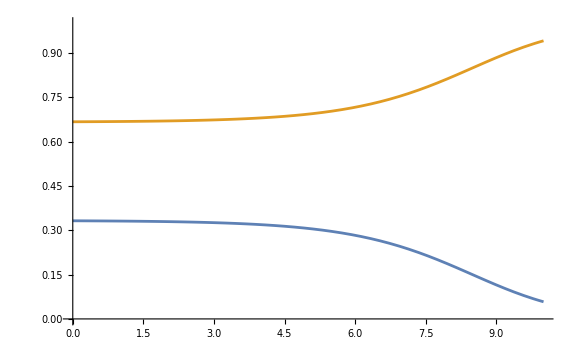

```mathematica
ClearAll[M,fA,fB,tmax,No,x,y];
M={{5,0},{3,1}};
x0=1/3-0.001;
phi[t]:=fA[x[t],y[t]]*x[t]+fB[x[t],y[t]]*y[t];
fA[x_,y_]:=( M[[1,1]]*x+M[[1,2]]*y);
fB[x_,y_]:=( M[[2,1]]*x+M[[2,2]]*y);
tmax=400;
soln=First@NDSolve[{x'[t]==fA[x[t],y[t]]*x[t]-phi[t]*x[t],y'[t]==fB[x[t],y[t]]*y[t]-phi[t]*y[t],x[0]==x0,y[0]==1-x[0]},{x,y},{t,0,tmax}];
P2=Plot[{x[t]/. soln,y[t]/. soln},{t,0,10},PlotRange->{0,1},ImageSize->Large]
(*Export["grafico_LZ2.pdf",P2];*)
```

## Zebras and Lions 3: Exactly in the equilibrium point. Here the computer makes a mistake for large simulation times (because the computer cannot represent 1/3 exactly, and it gives a very little advantage to zebras.

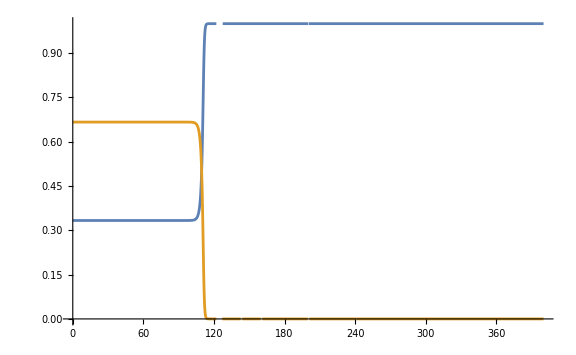

```mathematica
ClearAll[M,fA,fB,tmax,No,x,y];
M={{5,0},{3,1}};
x0=1/3;
phi[t]:=fA[x[t],y[t]]*x[t]+fB[x[t],y[t]]*y[t];
fA[x_,y_]:=( M[[1,1]]*x+M[[1,2]]*y);
fB[x_,y_]:=( M[[2,1]]*x+M[[2,2]]*y);
tmax=400;
soln=First@NDSolve[{x'[t]==fA[x[t],y[t]]*x[t]-phi[t]*x[t],y'[t]==fB[x[t],y[t]]*y[t]-phi[t]*y[t],x[0]==x0,y[0]==1-x[0]},{x,y},{t,0,tmax}];
P3=Plot[{x[t]/. soln,y[t]/. soln},{t,0,tmax},PlotRange->{0,1},ImageSize->Large]
(*Export["grafico_LZ3.pdf",P3]; *)
(*It should failt due to numerics, but for large time t*)
```